```mathematica
Quit
```

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
<<FunctionRepo`
```

### AggregateRowsByKey

```mathematica
<<FunctionRepo`
```

```mathematica
?AggregateRowsByKey
```

```mathematica
data=ExampleData[{"Dataset","Titanic"}];
```

```mathematica
AggregateRowsByKey[data,"age"->Median]
```

```mathematica
Values@GroupBy[data, {Lookup[#,{"sex","survived"}], #class==="3rd"}&,AggregateRowsByKey["age"->N@*Median]]
```

```mathematica
Values@GroupBy[data, {Lookup[#,{"sex","survived"}], #class==="3rd"}&,AggregateRowsByKey[{"age"->N@*Median,"class"->Counts}]]
```

### AssociationSet

```mathematica
?AssociationSet
```

```mathematica
assoc=<||>;
AssociationSet[assoc[1,2,3],"foo"];
assoc
```

```mathematica
AssociationSet[assoc[2,1,5,6,3],"foo"];
assoc
```

```mathematica
AssociationSet[assoc[2,1,5,7,3],"foo"];
assoc
```

### AssociationTemplate

```mathematica
<<FunctionRepo`
```

```mathematica
?AssociationTemplate
```

```mathematica
AssociationTemplate[]["a"]
```

```mathematica
AssociationTemplate[
<|
"a"->TemplateExpression[TemplateSlot["b"]],
"b"-> TemplateExpression[TemplateSlot["a"]] ,
"c"-> StringTemplate["`a` + `b`"]
|>
]
```

```mathematica
sAssoc=AssociationTemplate[
<|
"a"-> 3,
"b"-> TemplateExpression[NIntegrate[Abs@Sin[TemplateSlot["a"] x],{x,0,10}]] ,
"c"-> StringTemplate["The integral of |Sin[`a` x]| on 0 <= x <= 10 is `b`"]
|>
]
```

```mathematica
sAssoc=AssociationTemplate[
<|
"a"-> 3,
"b"-> Function[NIntegrate[Abs@Sin[#["a"] x],{x,0,10}]] ,
"c"-> StringTemplate["The integral of |Sin[`a` x]| on 0 <= x <= 10 is `b`"]
|>
]
```

```mathematica
sAssoc["a"]
sAssoc["b"]
sAssoc["c"]
```

```mathematica
Normal[sAssoc]
Keys[sAssoc]
Values[sAssoc]
Length[sAssoc]
```

```mathematica
sAssoc[["b"]]
sAssoc[[{"b","c"}]]
sAssoc[[2]]
sAssoc[[{2,3}]]
```

```mathematica
Join[sAssoc,<|"a"->3.|>]
%//Values
Append[sAssoc,"a" -> 3.]
%//Values
Prepend[sAssoc,"a" -> 3.]
%//Values
```

### AsynchronousDynamicModule

```mathematica
AsynchronousDynamicModule@DynamicModule[{x},Dynamic[First[x]],SynchronousInitialization->False,Initialization:>(x={};
Pause[3];
AppendTo[x,1])]
```

```mathematica
AsynchronousDynamicModule@DynamicModule[{x},Dynamic[Print["Hi!"];
First[x]],SynchronousInitialization->False,Initialization:>(x={};
Pause[3];
AppendTo[x,1])]
```

```mathematica
AsynchronousDynamicModule[DynamicModule[{x},Dynamic[x],SynchronousInitialization->False,Initialization:>(x={};
Pause[1];
AppendTo[x,1];
Pause[1];
AppendTo[x,2];
Pause[1];
AppendTo[x,3];
Pause[1];
AppendTo[x,4];)],Dynamic@ProgressIndicator[Length[x],{0,4}]]
```

```mathematica
AsynchronousDynamicModule[DynamicModule[{x,start,updateAction},Dynamic[Column[{x,Slider[Dynamic[start],{0,10,1}],Button["Update",updateAction[start],Method->"Queued",ImageSize->All]}]],SynchronousInitialization->False,Initialization:>(start=0;
updateAction[startVal_]:=(initQ=False;
x={};
Pause[1];
AppendTo[x,startVal+1];
Pause[1];
AppendTo[x,startVal+2];
Pause[1];
AppendTo[x,startVal+3];
Pause[1];
AppendTo[x,startVal+4];
initQ=True);
updateAction[start])],Dynamic@ProgressIndicator[Length[x],{0,4}],initQ]
```

### checkboxLegended

```mathematica
<<FunctionRepo`
```

```mathematica
dataset=<|"Dataset1"-> Range[10],"Dataset2"-> Range[10,1,-1]|>;
checkboxLegended[
ListPlot[dataset]
]
```

### conditionalProductDistribution

```mathematica
<<FunctionRepo`
```

```mathematica
conditionalProductDistribution::usage
```

```mathematica
conditionalProductDistribution[x\[Distributed]NormalDistribution[0,1]]
```

```mathematica
conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p]]
conditionalProductDistribution[k\[Distributed]BinomialDistribution[k,p]]
conditionalProductDistribution[p \[Distributed] BetaDistribution[α,β], k\[Distributed]BinomialDistribution[n,p]]
conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p], p \[Distributed] BetaDistribution[α,β]]
```

```mathematica
PDF[conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p],p \[Distributed] BetaDistribution[α,β]],{k,p}]
```

```mathematica
Likelihood[conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p],p \[Distributed] BetaDistribution[α,β]],{{k,p},{3,1/2}}]
LogLikelihood[conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p],p \[Distributed] BetaDistribution[α,β]],{{k,p},{3,1/2}}]
```

```mathematica
Graph@conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p],p \[Distributed] BetaDistribution[α,β]]
Graph@conditionalProductDistribution[l\[Distributed]GeometricDistribution[p/(k+1)],k\[Distributed]BinomialDistribution[n,p],p\[Distributed]BetaDistribution[α,β],n\[Distributed]GeometricDistribution[1/2]]
```

```mathematica
dist=conditionalProductDistribution[
l\[Distributed]GeometricDistribution[p/(k+1)],k\[Distributed]BinomialDistribution[n,p],
p\[Distributed]BetaDistribution[α+1,β+1],{n,α,β}\[Distributed]ProductDistribution[{GeometricDistribution[1/2],3}]
]
Graph[dist]
rv1=RandomVariate[dist]
rv2=RandomVariate[dist,3]
LogLikelihood[dist,rv2]
Likelihood[dist,rv2]
Log[%]==%%
PDF[dist,rv2]
Times@@%==%%%
PDF[dist,rv1]
Likelihood[dist,{rv1}]
%==%%
```

```mathematica
dist=conditionalProductDistribution[
l\[Distributed]GeometricDistribution[p/(k+1)],k\[Distributed]BinomialDistribution[v1,p],
p\[Distributed]BetaDistribution[v2+1,v3+1],v\[Distributed]ProductDistribution[{GeometricDistribution[1/2],3}]
]
Graph[dist]
rv1=RandomVariate[dist]
rv2=RandomVariate[dist,3]
LogLikelihood[dist,rv2]
Likelihood[dist,rv2]
Log[%]==%%
PDF[dist,rv2]
Times@@%==%%%
PDF[dist,rv1]
Likelihood[dist,{rv1}]
%==%%
```

```mathematica
Graph@conditionalProductDistribution[{a,b}\[Distributed]BinormalDistribution[{σ1,σ2},ρ],ρ\[Distributed]BetaDistribution[1,2],{σ1,σ2}\[Distributed]MultinormalDistribution[{10,10},{{1,0},{0,1}}]]
```

```mathematica
RandomVariate[conditionalProductDistribution[k\[Distributed]BinomialDistribution[10,p],p \[Distributed] BetaDistribution[1,2]]]
RandomVariate[conditionalProductDistribution[k\[Distributed]BinomialDistribution[10,p],p \[Distributed] BetaDistribution[1,2]],3]
RandomVariate[conditionalProductDistribution[k\[Distributed]BinomialDistribution[10,p],p \[Distributed] BetaDistribution[1,2]],{5,3}]
```

```mathematica
RandomVariate[conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p],p \[Distributed] BetaDistribution[1,2]]]
```

```mathematica
RandomVariate[conditionalProductDistribution[{a,b}\[Distributed]BinormalDistribution[{μ1,μ2},{1,2},0.3],{μ1,μ2} \[Distributed] BinormalDistribution[0.5]]]
RandomVariate[conditionalProductDistribution[{a,b}\[Distributed]BinormalDistribution[{μ1,μ2},{1,2},0.3],{μ1,μ2} \[Distributed] BinormalDistribution[0.5]],3]
RandomVariate[conditionalProductDistribution[{a,b}\[Distributed]BinormalDistribution[{μ1,μ2},{1,2},0.3],{μ1,μ2} \[Distributed] BinormalDistribution[0.5]],{5,3}]
```

```mathematica
RandomVariate[
conditionalProductDistribution[
x\[Distributed]MultinormalDistribution[μ,ν Σ],
ν\[Distributed]InverseGammaDistribution[5,10],
μ\[Distributed]MultinormalDistribution[{0,0},Σ],
Σ\[Distributed]InverseWishartMatrixDistribution[10,{{1,1/3},{1/3,1}}]
],
10
]
```

```mathematica
normalInverseWishartDistribution[μ0_,λ_,Ψ_,ν_]:= conditionalProductDistribution[
μ\[Distributed]MultinormalDistribution[μ0,Σ/λ],
Σ\[Distributed]InverseWishartMatrixDistribution[ν,Ψ]
];
```

```mathematica
RandomVariate[normalInverseWishartDistribution[{1,-3},5,({{1, 1/2}, {1/2, 2}}),7],5]
```

```mathematica
posterior[μ0_,λ_,Ψ_,ν_]:=conditionalProductDistribution[
X\[Distributed]MultinormalDistribution[μ,Σ],
{μ,Σ}\[Distributed]normalInverseWishartDistribution[μ0,λ,Ψ,ν]
]
```

```mathematica
RandomVariate[posterior[{1,-3},5,({{1, 1/2}, {1/2, 2}}),7],5]
```

### conditionedMultinormalDistribution

```mathematica
?conditionedMultinormalDistribution
```

```mathematica
dist=MultinormalDistribution[{μ1,μ2},{{Σ11,Σ12},{Σ12,Σ22}}];
conditionedMultinormalDistribution[dist,2->x2]
```

```mathematica
conditionedMultinormalDistribution[dist,2->x2,1]
```

### convertDataFormat

```mathematica
?convertDataFormat
```

### ConvertStringsToSymbols

```mathematica
?ConvertStringsToSymbols
```

```mathematica
x=1;
ConvertStringsToSymbols[
Unevaluated[
Print["x"];
"x"=2;
 Print["x"]
],
"x"
]
```

```mathematica
x=1;
ConvertStringsToSymbols[
Hold[
Print["x"];
"x"=2;
 Print["x"]
],
"x"
]
ReleaseHold[%]
```

```mathematica
x=1;
ConvertStringsToSymbols[Hold["x","y"],"x"]//FullForm
```

```mathematica
x=1;
ConvertStringsToSymbols[Hold["x","y"],"x"->"bla`"]//FullForm
```

```mathematica
ConvertStringsToSymbols[Hold["x","y"],{"x","y"}]//FullForm
```

```mathematica
ConvertStringsToSymbols[Hold["x","y"],{"x"->"bla`","y"}]//FullForm
```

```mathematica
ConvertStringsToSymbols[Hold["x","y"],{"x","y"}->"bla`"]//FullForm
```

### ConvertToTemplateNotebook

```mathematica
?ConvertToTemplateNotebook
```

```mathematica
ConvertToTemplateNotebook[]
```

### CopyAsExcelData

```mathematica
<<FunctionRepo`
```

```mathematica
?CopyAsExcelData
```

```mathematica
CopyAsExcelData[{1,"2",Now,Today, TimeObject[]}]
```

### CrossValidateModel

```mathematica
?CrossValidateModel
```

```mathematica
data = RandomVariate[PoissonDistribution[2],100];
Histogram[data,{1},PlotRange->All]
```

```mathematica
val=CrossValidateModel[data,PoissonDistribution[λ]];
val//TableForm
```

### DateAmbiguityBreak

```mathematica
?DateAmbiguityBreak
```

```mathematica
dates={"11-02-2022T15:30:24","12-02-2022","13-02-2022","14-02-2022","15-02-2022","16-02-2022","17-02-2022", "Feb 2 2020", "3 Feb 2021"};
DateAmbiguityBreak["DayFirst"]@dates
DateAmbiguityBreak["MonthFirst"]@dates
```

### deleteContainedStrings

```mathematica
?deleteContainedStrings
```

### ExpressionToFunction

```mathematica
?ExpressionToFunction
```

Create a function from a simple polynomial:

```mathematica
polyFun=ExpressionToFunction[1+2 x + x^2,x]
```

Evaluate the polynomial at a given value:

```mathematica
polyFun[1]
```

Convert a multivariate PDF to a function:

```mathematica
pdf = PDF[BinormalDistribution[1/3],{x,y}]
```

```mathematica
pdfFun=ExpressionToFunction[Evaluate[pdf],x,y]
```

```mathematica
N@pdfFun[0,1]
```

Bind x and y to the first slot of the function as a vector:

```mathematica
pdfFun2=ExpressionToFunction[Evaluate[pdf],{x,y}]
```

```mathematica
N@pdfFun2[{0,1}]
```

Bind arguments to keys in an Association:

```mathematica
powerFun=ExpressionToFunction[x^y,x->"Base",y-> "Exponent"]
```

```mathematica
powerFun[<|"Base"->2,"Exponent"->3|>]
```

Bind multiple symbols to a single slot:

```mathematica
ExpressionToFunction[x+y,{x,y}][{E, Pi}]
```

```mathematica
powerFun2=ExpressionToFunction[x^y,{x,y}->"BaseExponentTuple"]
```

```mathematica
powerFun2[<|"BaseExponentTuple"->{2,3}|>]
```

Combine names slots with positional slots:

```mathematica
powerFun3=ExpressionToFunction[z*x^y,z->"z",{x,y}->2]
```

```mathematica
powerFun3[<|"z"->Pi|>,{E,2}]
```

Use the Attributes option to return a function that holds its arguments:

```mathematica
addToSymbol=ExpressionToFunction[var=var+val,var,val,Attributes->HoldFirst]
```

```mathematica
counter=1
```

```mathematica
addToSymbol[counter,2]
```

```mathematica
counter
```

Group x and y together as a vector argument and map over a list of points:

```mathematica
pdf = PDF[BinormalDistribution[1/3],{x,y}]
```

```mathematica
pdfVectorFun=ExpressionToFunction[Evaluate[pdf],{x,y}]
```

```mathematica
dataRange = {{-3,3},{-3,3}};
```

```mathematica
points=Map[pdfVectorFun, CoordinateBoundsArray[dataRange,0.1],{2}];
```

```mathematica
ListContourPlot[points,DataRange->dataRange]
```

Add a parameter of the PDF as an argument:

```mathematica
parameterizedPDF=ExpressionToFunction[
Evaluate[
PDF[BinormalDistribution[ρ],{x,y}]
],
{x,y},
ρ
]
```

```mathematica
parameterizedPDF[{2,1},1/10]
```

Convert the solution of a differential equation to a function:

```mathematica
sol = DSolveValue[{y'[x]+y[x]==a Sin[x],y[0]==0},y[x],x]
```

```mathematica
dSolveFun=ExpressionToFunction[Evaluate[sol],x,a]
```

```mathematica
dSolveFun[10,1]
```

Represent the function at parameter value a=10 with Curry, then map over a range of x-values:

```mathematica
AssociationMap[
Curry[dSolveFun][10],
Range[0,10,0.1]
]//ListPlot
```

### FileTreePicker

```mathematica
?FileTreePicker
```

```mathematica
FileTreePicker[Dynamic[files]]
```

### FindXMLTableData

```mathematica
?FindXMLTableData
```

### firstMatchingValue

```mathematica
?firstMatchingValue
```

```mathematica
firstMatchingValue[{Print["before"],10,Print["after"]},_Integer]
```

```mathematica
x=2;
{x,
firstMatchingValue[{a,2,++x,1+3,5},_Integer?OddQ],
x}
```

### FunctionArgumentCount

```mathematica
?FunctionArgumentCount
```

Find the highest numbered slot in a function:

```mathematica
FunctionArgumentCount[Function[#^2]]
```

```mathematica
FunctionArgumentCount[Function[#1 + #2]]
```

```mathematica
FunctionArgumentCount[Function[{x,y,z},Sin[x + y/z]]]
```

In this function, slot 2 goes unused, but it will still be counted:

```mathematica
FunctionArgumentCount[Function[#1 + #3]]
```

Slots in inner functions will not be counted:

```mathematica
FunctionArgumentCount[
Function[
Function[#1+#2+#3][#1,2#1,3#1]
]
]
```

A function that uses SlotSequence will be counted as having infinite arguments:

```mathematica
FunctionArgumentCount[Function[Plus[##]]]
```

String slots will be counted as being part of the first argument:

```mathematica
FunctionArgumentCount[Function[#a  + #b]]
```

```mathematica
FunctionArgumentCount[Function[#a  + #b+#2]]
```

FunctionArgumentCount works with compiled functions:

```mathematica
FunctionArgumentCount[Compile[{x,y,z},Sqrt[x y z]]]
```

A function that uses SlotSequence will be counted as having infinite arguments:

```mathematica
FunctionArgumentCount[Function[Plus[#1, #2,##]]]
```

This behavior can be changed with the "IgnoreSlotSequence" option:

```mathematica
FunctionArgumentCount[Function[Plus[#1,#2, ##]], "IgnoreSlotSequence"-> True]
```

### FunctionToExcelFormula

```mathematica
<<FunctionRepo`
```

```mathematica
?FunctionToExcelFormula
```

```mathematica
FunctionToExcelFormula[RandomReal,"A1"]
%//CopyToClipboard
```

```mathematica
FunctionToExcelFormula[ConstantArray[#1,#2]&,{"A1","B1"}]
%//CopyToClipboard
```

```mathematica
FunctionToExcelFormula[Function[nans,StringJoin[ConstantArray["NA",nans]]<>" BATMAN"],"A1"]
%//CopyToClipboard
```

### graphicsToGraph

```mathematica
?graphicsToGraph
```

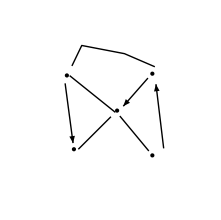
```mathematica
graph=graphicsToGraph[
-Graphics-
]
```

### GroupCases

```mathematica
<<FunctionRepo`
```

```mathematica
?GroupCases
```

```mathematica
GroupCases[{1,2,3.,x},_Integer]
```

```mathematica
GroupCases[{1,2,3.,x},i_Integer:>i/2]
```

```mathematica
GroupCases[{1,2,3.,x,4},i_Integer:>With[{j=i/2},j/;EvenQ[j]]]
```

```mathematica
GroupCases[{1,2,3.,x},{_Integer,_Real}]
```

```mathematica
GroupCases[{1,2,3.,x},<|"Int"-> _Integer,"Float"-> _Real,"NAN"-> _|>]
```

```mathematica
GroupCases[{1,2,3.,x},{_Integer,_Real,_Complex}]
```

```mathematica
test=RandomChoice[{1,1.},10^3];
GroupBy[test,IntegerQ];//RepeatedTiming
GroupCases[test,_Integer];//RepeatedTiming
```

### ImageLocatorPaneWithZoom

```mathematica
?ImageLocatorPaneWithZoom
```

```mathematica
<<FunctionRepo`
```

```mathematica
img=ExampleData[{"TestImage","Stall"}];
img=ImageResize[img,1000]
```

```mathematica
pts={};
ImageLocatorPaneWithZoom[Dynamic[pts],
Image[img,ImageSize->Full],
 LocatorAutoCreate->{All, {0,3}}
]
```

```mathematica
pts={};
ImageLocatorPaneWithZoom[Dynamic[pts],
Show[Image[img,ImageSize->Full], Graphics[Dynamic@Line[pts]]],
 LocatorAutoCreate->{All, {0,3}},
"ShowZoomControls"->False,"ZoomLevel"->2,
"ZoomSize"->0.15,"MarkerFunction"->Automatic,
"MarkerColor"->Red,"ShowCoordinates"->True
]
```

### KeyComplete

```mathematica
?KeyComplete
```

### kullbackLeiblerDivergence

```mathematica
?kullbackLeiblerDivergence
```

```mathematica
kullbackLeiblerDivergence[BinormalDistribution[ρ1],BinormalDistribution[ρ2]]
```

```mathematica
kullbackLeiblerDivergence[
EmpiricalDistribution[{"a","b","b"}],
EmpiricalDistribution[{"a","b","c"}]
]
```

```mathematica
kullbackLeiblerDivergence[
BernoulliDistribution[p],
EmpiricalDistribution[{0,0,1}]
]
```

### LogSumExpLayer

```mathematica
<<FunctionRepo`
```

```mathematica
?LogSumExpLayer
```

```mathematica
matrix=RandomReal[1,{2,3,4,5}];
LogSumExpLayer[]@matrix
Dimensions[%]
```

```mathematica
LogSumExpLayer[{2}]@matrix
Dimensions[%]
```

```mathematica
LogSumExpLayer[All]@matrix
Dimensions[%]
```

### maximumSpacingEstimation

```mathematica
?maximumSpacingEstimation
```

### MergeByKey

```mathematica
<<FunctionRepo`
```

```mathematica
?MergeByKey
```

```mathematica
MergeByKey[{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>},a->Total]
```

```mathematica
MergeByKey[{}, {}]
MergeByKey[{}, {a->1}]
MergeByKey[{}, {a->1},f]
MergeByKey[{}]@{}
MergeByKey[{a->1}]@{}
MergeByKey[{a->1},f]@{}
```

```mathematica
MergeByKey[{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>},{a->Total,b->RootMeanSquare}]
MergeByKey[{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>},{a->Total,b->RootMeanSquare,c-> foo}]
MergeByKey[{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>},{a->Total,b->RootMeanSquare},foo]
```

```mathematica
MergeByKey[{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>},{Key[a]->Total,b->RootMeanSquare}]
MergeByKey[{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>},{Key[a]->Total,b->RootMeanSquare},foo]
```

```mathematica
MergeByKey[{a->Total,b->RootMeanSquare}]@{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>}
MergeByKey[{a->Total,b->RootMeanSquare,c-> foo}]@{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>}
MergeByKey[{a->Total,b->RootMeanSquare},foo]@{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>}
```

```mathematica
MergeByKey[{<|a->1,b->2|>,<|a->5,b->10,c-> Pi|>,<|c->E|>},{{a,b}-> Total, c-> Mean}]
MergeByKey[{<|a->1,b->2|>,<|a->5,b->10,c-> Pi|>,<|c->E|>},{{a,b}-> Total},Mean]
MergeByKey[{<|a->1,b->2|>,<|a->5,b->10,c-> Pi|>,<|c->E|>},{c-> Mean},Total]
```

```mathematica
MergeByKey[{<|{a}->1,b->2|>,<|{a}->5,b->10|>},{{a}-> Total}]
MergeByKey[{<|{a}->1,b->2|>,<|{a}->5,b->10|>},{Key[{a}]-> Total}]
MergeByKey[{<|{a}->1,b->2|>,<|{a}->5,b->10|>},{{Key[{a}],b}-> Total}]
```

### MergeByKeyNested

```mathematica
<<FunctionRepo`
```

```mathematica
?MergeByKeyNested
```

```mathematica
MergeByKeyNested[{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>},{a->Total,b->RootMeanSquare},foo]
```

```mathematica
MergeByKeyNested[{<|1-><|a->1,b->2|>|>,<|1-><|b->5,c-> Pi|>|>,<|2-><|a->5,b->10|>|>},{a->f,b->g},foo]
```

### MergeNested

```mathematica
<<FunctionRepo`
```

```mathematica
?MergeNested
```

```mathematica
MergeNested[{}, f]
```

```mathematica
MergeNested[{<|a->1|>,<|a->2|>}, f]
```

```mathematica
MergeNested[{<|a-><|b->1|>|>,<|a-><|b->2,c->3|>|>}, f]
```

```mathematica
MergeNested[{<|a-><|b->1|>|>,<|a->3|>}, f]
```

### MultiNonlinearModelFit

```mathematica
?MultiNonlinearModelFit
```

```mathematica
data=RandomVariate[BinormalDistribution[0.7],{2,100}];
data[[2,All,2]]+=2.;

model=MultiNonlinearModelFit[
data,
 {a x+ b1,a x + b2},{a,b1,b2},
{x}
]
```

```mathematica
Show[
ListPlot[data],
Plot[Evaluate[Table[Normal[model],{n,Length[data]}]],{x,-5,5}]
]
```

### multiSet

```mathematica
<<FunctionRepo`
```

```mathematica
?multiSet
```

```mathematica
Union[multiSet[{1,1,2}],multiSet[{2,2,1,3}]]//Normal
```

```mathematica
Intersection[multiSet[{1,1,2,3,3}],multiSet[{1,1,1,3}]]
```

```mathematica
Values@Complement[multiSet[{1,1,2}],multiSet[<|1->n,2->2,3->1|>]]
```

### MonitorFile

```mathematica
?MonitorFile
Options[MonitorFile]//TableForm
```

```mathematica
MonitorFile[
Dynamic[contents],
FileNameJoin[{NotebookDirectory[],"FunctionRepo","Kernel","MonitorFile.wl"}],
"ImportFunction"->Function[Import[#,"String"]]
]
```

```mathematica
Dynamic[contents]
```

```mathematica
MonitorFile[
Dynamic[contents],
FileNameJoin[{NotebookDirectory[],"FunctionRepo","Kernel","MonitorFile.wl"}],
"ImportFunction"->Function[Import[#,{"WL","HeldExpressions"}]],
"ContentDisplayFunction"->Function[First[#,""]],
"LayoutFunction" -> Function[{file,date,contentDisplay},Column[{file,date,Framed[contentDisplay]}]]
]
```

### OpenTestWritingPalette

```mathematica
<<FunctionRepo`
```

```mathematica
?OpenTestWritingPalette
```

```mathematica
OpenTestWritingPalette[]
```

### PositionQ

```mathematica
?PositionQ
```

```mathematica
PositionQ[{1},{1}]
PositionQ[{1},{2}]
```

```mathematica
PositionQ[{1,2},{{1}}]
PositionQ[{1,2},{{1},{2}}]
PositionQ[{1,2},{{1},{3}}]
```

```mathematica
PositionQ[{1,2},{1,2,3}]
PositionQ[{1,2},{{1,2,3}}]
```

```mathematica
PositionQ[1+1,{1}]
PositionQ[Unevaluated[1+1],{1}]
```

### QuantityString

```mathematica
?QuantityString
```

```mathematica
<<FunctionRepo`
```

```mathematica
q=Quantity[1.24,(("Millimeters")^3"Kelvins")/("Kilograms" ("Seconds")^2)];
QuantityString[q]
QuantityString[q,"Canonical"]
QuantityString[q,"`1` `2` (`3`)"]
```

```mathematica
Quantity[2.5,#]&/@{"Yen","Euros","USDollars","Rubles"}
QuantityString/@%
```

### ScalableContentWindow

```mathematica
?ScalableContentWindow
```

```mathematica
<<FunctionRepo`
```

```mathematica
ScalableContentWindow[Graphics[Disk[]]]
```

```mathematica
ScalableContentWindow[
Block[{x},
Plot[Evaluate@Table[Labeled[x^n,x^n],{n,1,3}],{x,-3,3},PlotLabel->"Polynomials"]
]
]
```

```mathematica
ScalableContentWindow[
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{{a,1},ControlType->InputField}]
]
```

### SparseAssociation

```mathematica
SparseAssociation::usage
```

```mathematica
array=RandomInteger[2,{4,2,3}]
```

```mathematica
sparseAssoc=SparseAssociation[SparseArray[array,Automatic,1],{"a","b","c","d"},0]
```

```mathematica
sparseAssoc===SparseAssociation[Normal[sparseAssoc],Keys[sparseAssoc]]
```

```mathematica
Normal@Values@sparseAssoc===array
```

```mathematica
Length[sparseAssoc]
ArrayDepth[sparseAssoc]
Dimensions[sparseAssoc]
Keys[sparseAssoc]
```

```mathematica
sparseAssoc["a","b","c"]
%===array[[1,2,3]]
```

```mathematica
sparseAssoc[["a",All, {1, 3}]]===sparseAssoc[[1,All,{"a","c"}]]
```

```mathematica
sparseAssoc[["b",All,{"a","c"}]]
Normal@Values@%===array[[2,All,{1,3}]]
```

```mathematica
Map[#^2&,sparseAssoc,{3}]
Normal@Normal[%]
```

```mathematica
ArrayRules@sparseAssoc
```

```mathematica
SparseAssociation[RandomInteger[2,{3,3,3}],Partition[Take[Alphabet[],9],3]]
ArrayRules[%]
```

### SplitAt

```mathematica
<<FunctionRepo`
```

```mathematica
?SplitAt
```

```mathematica
SplitAt[
{5,7,3,4,5,5,3,7,8,9,1,8,7,9,10,2,10,4,1},
EvenQ
]
```

```mathematica
SplitAt[
{5,7,3,4,5,5,3,7,8,9,1,8,7,9,10,2,10,4,1},
EvenQ,
After
]
```

### SplitAtPositions

```mathematica
<<FunctionRepo`
```

```mathematica
?SplitAtPositions
```

```mathematica
SplitAtPositions[Range[20],{1,4,10,20},Before]
```

```mathematica
SplitAtPositions[Range[20],{1,4,10,20},After]
```

```mathematica
SplitAtPositions[Range[20],{1,4,10,0},After]
```

### SymbolicSort

```mathematica
?SymbolicSort
```

```mathematica
<<FunctionRepo`
```

```mathematica
SymbolicSort[{Exp[x],x},x]
```

```mathematica
SymbolicSort[{x,Log[x],Exp[x],x^2+1},x,x>0]
SymbolicSort[{x,Log[x],Exp[x],x^2+1},x,x>0,Reals,Graph]
```

```mathematica
SymbolicSort[{x,√(x^2)},x,x>0]
SymbolicSort[{√(x^2),x},x,x>0]
```

```mathematica
SymbolicSort[{Exp[y],Exp[x],Exp[z]},{x,y,z},x<y<z]
SymbolicSort[{Exp[y],Exp[x],Exp[z]},{x,y,z},x<y<z,Reals,Graph]
```

```mathematica
SymbolicSort[{y,Log[x],Exp[z]},{x,y,z},0<x<y<z]
SymbolicSort[{y,Log[x],Exp[z]},{x,y,z},0<x<y<z,Reals,Graph]
```

```mathematica
SymbolicSort[{Exp[y],x,Exp[z],a},{x,y,z,a},0<x<y<z]
SymbolicSort[{Exp[y],x,Exp[z],a},{x,y,z,a},0<x<y<z,Reals,Graph]
```

```mathematica
SymbolicSort[{x,Log[x],Exp[x],x^2+1,Sin[x]},x,x>0,Reals,Graph]
```

### TimedPaneSelector

```mathematica
<<FunctionRepo`
```

```mathematica
?TimedPaneSelector
```

```mathematica
state=1;
TimedPaneSelector[{1->1,2->2},Dynamic[state],{1->2,2->1},"ResetTime"-><|1->1,2->3|>]
```

```mathematica
state=1;
Clear[t];
TimedPaneSelector[{1->1,2->2},{Dynamic[state],Dynamic[t]},{1->2,2->1},"ResetTime"-><|1->1,2->3|>,UpdateInterval->0.1]
Dynamic[t]
```

```mathematica
state=1;
Clear[t];
TimedPaneSelector[{1->1,_->2},{Dynamic[state],Dynamic[t]},{1->2},"ResetTime"-><|1->1,2->3|>,UpdateInterval->0.1]
Dynamic[t]
```

```mathematica
state=1;
Clear[t];
spec=<|1->1,2->3|>;
TimedPaneSelector[{1->1,2->2},{Dynamic[state],Dynamic[t]},{1->2,2->1},"ResetTime"->Dynamic[spec],UpdateInterval->0.1]
Dynamic[t]
```

### ToExpressionExpect

```mathematica
?ToExpressionExpect
```

```mathematica
<<FunctionRepo`
```

```mathematica
ToExpressionExpect["1+1",_Plus,Automatic,f]
```

```mathematica
ToExpressionExpect["1+1",_Plus,Automatic,Hold]
```

```mathematica
ToExpressionExpect["1+1",_Times,Automatic,Hold]
```

```mathematica
ToExpressionExpect[RowBox[{"1","+","1"}],_Plus,Automatic]
```

```mathematica
ToExpressionExpect[RowBox[{"1","+","1"}],_Integer]
```

### tukeyMedianPolish

```mathematica
?tukeyMedianPolish
```

```mathematica
matrix=N@RandomInteger[10,{4,6}];
Grid[matrix]
```

```mathematica
polish = tukeyMedianPolish[matrix];
Grid[polish,Dividers->{-2->True,-2->True}]
```

### WithCachedValues

```mathematica
?WithCachedValues
```

```mathematica
<<FunctionRepo`
```

```mathematica
ClearAll[f]
f[x_]/;EvenQ[x] :=(Pause[1];Print[{x}];Cos[x]);
f[x_] :=(Pause[1];Print[x];Sin[x]);
f[args___] :=(Pause[1];Print[{args}];Sin[{args}]);
```

```mathematica
WithCachedValues[{f,g},{f[1],f[1],f[2],f[1],f[2],f[1],f[2],f[1,2],f[1,2]}]//AbsoluteTiming
```

```mathematica
DownValues[f]//TableForm
```

### WLTToNotebook

```mathematica
?WLTToNotebook
```